```mathematica
pauilGroup = {IdentityMatrix[2],{{1,0},{0,-1}},{{0,I},{I,0}},{{0,-1},{1,0}}};
```

```mathematica
pauilGroup
```

{{{1,0},{0,1}},{{1,0},{0,-1}},{{0,ⅈ},{ⅈ,0}},{{0,-1},{1,0}}}

```mathematica
result = Table[play[J[a,b,γ],p1,p2],{p1,pauilGroup},{p2,pauilGroup}
];
```

```mathematica
postEntanglement = Table[
EntanglementMeasure[result[[i,j]]],{i,4},{j,4}
];
```

```mathematica
postEntanglement//Simplify//FullSimplify//ExpToTrig//FullSimplify//MatrixForm
```

(0 | (-2 Cos[2 γ] Log[Cot[γ]]+Log[4 Csc[2 γ]^2])/Log[4] | (-2 Cos[2 γ] Log[Cot[γ]]+Log[4 Csc[2 γ]^2])/Log[4] | 0
-(2 (Cos[γ]^2 Log[Cos[γ]]+Log[Sin[γ]] Sin[γ]^2))/Log[2] | 0 | 0 | -(2 (Cos[γ]^2 Log[Cos[γ]]+Log[Sin[γ]] Sin[γ]^2))/Log[2]
-(2 (Cos[γ]^2 Log[Cos[γ]]+Log[Sin[γ]] Sin[γ]^2))/Log[2] | 0 | 0 | -(2 (Cos[γ]^2 Log[Cos[γ]]+Log[Sin[γ]] Sin[γ]^2))/Log[2]
0 | (-2 Cos[2 γ] Log[Cot[γ]]+Log[4 Csc[2 γ]^2])/Log[4] | (-2 Cos[2 γ] Log[Cot[γ]]+Log[4 Csc[2 γ]^2])/Log[4] | 0)

```mathematica
result/.{a->Pi,γ->Pi/4,b->Pi}//ComplexExpand//FullSimplify//MatrixForm
```

((1
0
0
0) | (1/(√2)
1/(√2)
0
0) | (0
1
0
0) | (-1/(√2)
1/(√2)
0
0) | (-1
0
0
0) | (-1/(√2)
-1/(√2)
0
0) | (0
-1
0
0) | (1/(√2)
-1/(√2)
0
0)
(1/(√2)
0
1/(√2)
0) | (1/2
1/2
1/2
1/2) | (0
1/(√2)
0
1/(√2)) | (-1/2
1/2
-1/2
1/2) | (-1/(√2)
0
-1/(√2)
0) | (-1/2
-1/2
-1/2
-1/2) | (0
-1/(√2)
0
-1/(√2)) | (1/2
-1/2
1/2
-1/2)
(0
0
1
0) | (0
0
1/(√2)
1/(√2)) | (0
0
0
1) | (0
0
-1/(√2)
1/(√2)) | (0
0
-1
0) | (0
0
-1/(√2)
-1/(√2)) | (0
0
0
-1) | (0
0
1/(√2)
-1/(√2))
(-1/(√2)
0
1/(√2)
0) | (-1/2
-1/2
1/2
1/2) | (0
-1/(√2)
0
1/(√2)) | (1/2
-1/2
-1/2
1/2) | (1/(√2)
0
-1/(√2)
0) | (1/2
1/2
-1/2
-1/2) | (0
1/(√2)
0
-1/(√2)) | (-1/2
1/2
1/2
-1/2)
(-1
0
0
0) | (-1/(√2)
-1/(√2)
0
0) | (0
-1
0
0) | (1/(√2)
-1/(√2)
0
0) | (1
0
0
0) | (1/(√2)
1/(√2)
0
0) | (0
1
0
0) | (-1/(√2)
1/(√2)
0
0)
(-1/(√2)
0
-1/(√2)
0) | (-1/2
-1/2
-1/2
-1/2) | (0
-1/(√2)
0
-1/(√2)) | (1/2
-1/2
1/2
-1/2) | (1/(√2)
0
1/(√2)
0) | (1/2
1/2
1/2
1/2) | (0
1/(√2)
0
1/(√2)) | (-1/2
1/2
-1/2
1/2)
(0
0
-1
0) | (0
0
-1/(√2)
-1/(√2)) | (0
0
0
-1) | (0
0
1/(√2)
-1/(√2)) | (0
0
1
0) | (0
0
1/(√2)
1/(√2)) | (0
0
0
1) | (0
0
-1/(√2)
1/(√2))
(1/(√2)
0
-1/(√2)
0) | (1/2
1/2
-1/2
-1/2) | (0
1/(√2)
0
-1/(√2)) | (-1/2
1/2
1/2
-1/2) | (-1/(√2)
0
1/(√2)
0) | (-1/2
-1/2
1/2
1/2) | (0
-1/(√2)
0
1/(√2)) | (1/2
-1/2
-1/2
1/2))

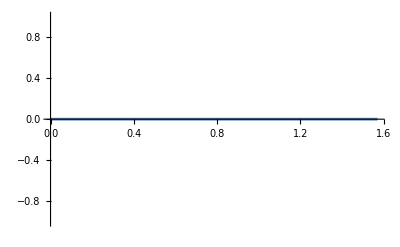
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[Plot[postEntanglement[[i,j]]/.γ->G,{G,0,Pi/2}],{i,4},{j,4}]
```

```mathematica
postEntanglement/((-2 Cos[2 γ] Log[Cot[γ]]+Log[4 Csc[2 γ]^2])/Log[4])//TrigReduce//FullSimplify//MatrixForm
```

(0 | 1 | 1 | 0
1 | 0 | 0 | 1
1 | 0 | 0 | 1
0 | 1 | 1 | 0)

```mathematica
entanglement//TrigReduce
```

(Log[4 Csc[γ]^2]+2 Cos[γ] Log[Tan[γ/2]])/Log[4]

```mathematica
(2 Cos[2 γ] Log[Tan[γ]]+Log[4 Csc[2 γ]^2])/Log[4]==(-2 Cos[2 γ] Log[Cot[γ]]+Log[4 Csc[2 γ]^2])/Log[4]
```

(Log[4 Csc[2 γ]^2]+2 Cos[2 γ] Log[Tan[γ]])/Log[4]==(-2 Cos[2 γ] Log[Cot[γ]]+Log[4 Csc[2 γ]^2])/Log[4]

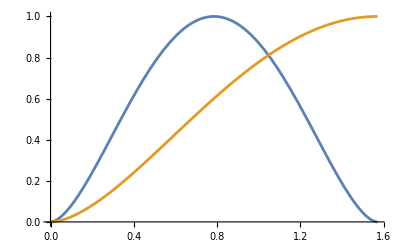

```mathematica
Plot[{(-2 Cos[2 γ] Log[Cot[γ]]+Log[4 Csc[2 γ]^2])/Log[4],entanglement},{γ,0,Pi/2}]
```

```mathematica
EntangledState
```

{1/4 (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)+ⅇ^(ⅈ (1+a+b) γ)),1/4 ⅈ (ⅇ^(ⅈ γ)-ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ)),1/4 ⅈ (ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)-ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ)),1/4 (-ⅇ^(ⅈ γ)+ⅇ^(ⅈ a γ)+ⅇ^(ⅈ b γ)-ⅇ^(ⅈ (1+a+b) γ))}

```mathematica
(mat)//FullSimplify//MatrixForm
```

(0 | (-2 Cos[2 γ] Log[Cot[γ]]+Log[4 Csc[2 γ]^2])/Log[4] | 0 | (-2 Cos[2 γ] Log[Cot[γ]]+Log[4 Csc[2 γ]^2])/Log[4]
-(2 (Cos[γ]^2 Log[Cos[γ]]+Log[Sin[γ]] Sin[γ]^2))/Log[2] | 0 | -(2 (Cos[γ]^2 Log[Cos[γ]]+Log[Sin[γ]] Sin[γ]^2))/Log[2] | 0
0 | (-2 Cos[2 γ] Log[Cot[γ]]+Log[4 Csc[2 γ]^2])/Log[4] | 0 | (-2 Cos[2 γ] Log[Cot[γ]]+Log[4 Csc[2 γ]^2])/Log[4]
-(2 (Cos[γ]^2 Log[Cos[γ]]+Log[Sin[γ]] Sin[γ]^2))/Log[2] | 0 | -(2 (Cos[γ]^2 Log[Cos[γ]]+Log[Sin[γ]] Sin[γ]^2))/Log[2] | 0)